# Jacobi Polynomials

By Manuel A. Diaz, NTU, 2012.07.29

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

#### Change Notebook BackGround

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255]]
```

## Jacobi Polynomials and beyond

### Initialize Notation

```mathematica
Needs["Notation`"]
```

based on http://en.wikipedia.org/wiki/Gram-Schmidt_process, we configure:

```mathematica
Notation[<a_,b_> ⟹ Integrate[a_ b_,{x,-1,1}]]
```

```mathematica
Notation[Subscript[proj, u_][v_] ⟹ (<u_,v_>)/(<u_,u_>)u_]
```

Testing:

```mathematica
<Subscript[v, 1][z],Subscript[v, 1][z]>
```

2 v_1[z]^2

```mathematica
<a z,z>
```

2 a z^2

```mathematica
(<a[z],b[z]>)/(<a[z],a[z]>)a[z] == Subscript[proj, a[z]][b[z]]
```

True

```mathematica
Symbolize[Subscript[Δx, j]]; Symbolize[Subscript[x, j]];Symbolize[Subscript[I, j]];
```

### Introduction

In the following we review the classical Jacobi Polynomials P_n^(α,β)(x), of order n is a solution to the singular Strum-Liouville eigenvalue problem

∂_x (1-x^2)w[x]∂_x P_n^(α,β)[x]+n(n+α+β+1)w(x)P_n^(α,β)[x]=0

for x ∈ [-1,1], where the weight function,  w[x]=(1-x)^α(1+x)^β.  w-Weigthed orthogonality are normalized to be orthonormal:

While there is not known simple expresion to evaluate the Jacobi Polynimials, it is conveniently done using the recurrence relation

x P_n^(α,β)[x] = a_n(P_(n-1))^(α,β)[x] +b_n P_n^(α,β)[x]+a_(n+1)(P_(n+1))^(α,β)[x]

where the coeficients are given as

```mathematica
a[n_,α_,β_]:= 2/(2n+α+β)√((n(n+α+β)(n+α)(n+β))/((2n+α+β-1)(2n+α+β+1)))
b[n_,α_,β_]:= -(α^2-β^2)/((2n+α+β)(2n+α+β+2))
```

```mathematica
{ a[n,α,β],b[n,α,β],a[n,0,0],b[n,0,0]}/.n->1 (* observe that n ≥ 1 to avoid errors in recurrence *)
```

{(2 √(((1+α) (1+β))/(3+α+β)))/(2+α+β),-(α^2-β^2)/((2+α+β) (4+α+β)),1/(√3),0}

To get the recurrence started, we need the initial values

```mathematica
Subscript[P, 0]= √(2^(-α-β-1)Gamma[α+β+2]/(Gamma[α+1]Gamma[β+1]));
Subscript[P, 1]=1/2 Subscript[P, 0] √((α+β+3)/((α+1)(β+1)))((α+β+2)x+(α+β));
```

```mathematica
{Subscript[P, 0],Subscript[P, 1]}
```

{√((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])),1/2 √((3+α+β)/((1+α) (1+β))) (α+β+x (2+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β]))}

let us compute the second term using the recurrence relation,

```mathematica
Subscript[P, 2]= (x Subscript[P, n] - a[n,α,β] Subscript[P, n-1] -b[n,α,β] Subscript[P, n])/a[n+1,α,β]/.n->1;
```

```mathematica
Subscript[P, 2]
```

1/(2 √2 √(((2+α) (2+β) (2+α+β))/((3+α+β) (5+α+β))))(4+α+β) (-(2 √(((1+α) (1+β))/(3+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])))/(2+α+β)+1/2 x √((3+α+β)/((1+α) (1+β))) (α+β+x (2+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β]))+(√((3+α+β)/((1+α) (1+β))) (α^2-β^2) (α+β+x (2+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])))/(2 (2+α+β) (4+α+β)))

### Generate Legendre Polynomials

Now lets compute the first 5 legendre polynomials assuming,

```mathematica
ClearAll[α,β,Np,n,x,polynomials,jacobiPolynomials]
```

```mathematica
α = 0;
β = 0;
```

```mathematica
polynomials = Table[Subscript[P, n+1]= (x Subscript[P, n] - a[n,α,β] Subscript[P, n-1] -b[n,α,β] Subscript[P, n])/a[n+1,α,β],{n,1,5}];
jacobiPolynomials = Join[{Subscript[P, 0],Subscript[P, 1]},polynomials] //Simplify //TableForm
```

1/(√2)
√(3/2) x
1/2 √(5/2) (-1+3 x^2)
1/2 √(7/2) x (-3+5 x^2)
(3 (3-30 x^2+35 x^4))/(8 √2)
1/8 √(11/2) x (15-70 x^2+63 x^4)
1/16 √(13/2) (-5+105 x^2-315 x^4+231 x^6)

Let’s examing their orthogonality property

```mathematica
Table[(<Subscript[P, i],Subscript[P, j]>),{i,0,6},{j,0,6}] //TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1

Wow! they are already orthonormal Legendre Polynomials!

```mathematica
ClearAll[α,β,Np,n,x,polynomials,jacobiPolynomials]
```

## Quadrilateral and tethahedral Elements

For these elements a simple dimension-by-dimension approach suffices. This technique is then called tenso product and in the case of representing u(x,y) in a quadrilateral in the domain [-1,1]^2, one can use legendre expansion and simply perform:

u_h[x,y]=∑_(i,j=0)^N OverHat[u_ij] P_i P_j

## On T^2Element

The construction of and orthonormal polynomial on a two-dimensional simplex,

T^2= {(r,s)|r,s≥-1,r+s≤ 0}

```mathematica
ClearAll[Simplex2D]
```

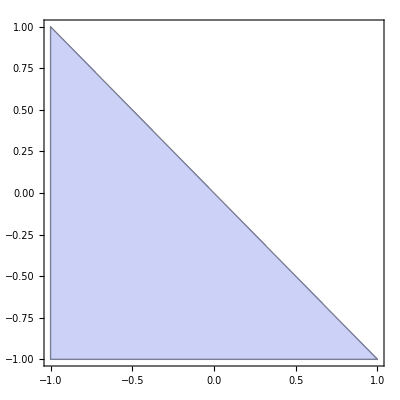

```mathematica
Simplex2D = RegionPlot[r≥-1 && s≥ -1 && s+r≤0,{r,-1,1},{s,-1,1}]
```

The N-th-order Orthonormal basis is given as,

```mathematica
Ndeg = 2;
```

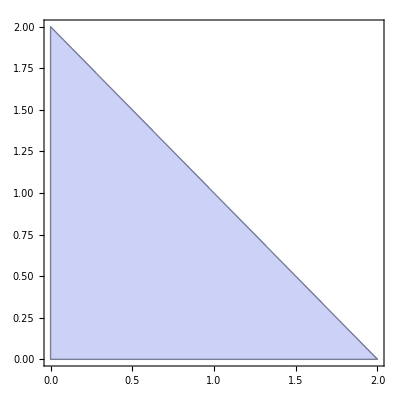

```mathematica
RegionPlot[i≥0&&j≥0&&i+j≤Ndeg,{i,0,Ndeg},{j,0,Ndeg}]
```

The number of terms in the polynomial is,

```mathematica
termsNumber = ((Ndeg+1)(Ndeg+2))/2
```

6

Using extended coordinates (a,b) ∈ [-1,1]^2 that relates to (s,r) ∈ T^2,

```mathematica
a[r_,s_]:= 2 (1+r)/(1-s)-1 
b[r_,s_]:= s
```

```mathematica
polynomials = Table[Subscript[P, n+1]= (x Subscript[P, n] - a[n,α,β] Subscript[P, n-1] -b[n,α,β] Subscript[P, n])/a[n+1,α,β],{n,1,3}];
jacobiPolynomials = Join[{Subscript[P, 0],Subscript[P, 1]},polynomials] //Simplify//TableForm
```

√((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β]))
1/2 √((3+α+β)/(1+α+β+α β)) (α+β+x (2+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β]))
((4+α+β) (-(4 √(((1+α) (1+β))/(3+α+β)))/(2+α+β)+x √((3+α+β)/(1+α+β+α β)) (α+β+x (2+α+β))+(√((3+α+β)/(1+α+β+α β)) (α^2-β^2) (α+β+x (2+α+β)))/((2+α+β) (4+α+β))) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])))/(4 √2 √(((2+α) (2+β) (2+α+β))/((3+α+β) (5+α+β))))
((6+α+β) (-(8 (2+α) (2+β) (2+α+β) √((3+α+β)/(1+α+β+α β)) (α+β+x (2+α+β)))/((3+α+β) (4+α+β) (5+α+β))+x (4+α+β) (-(4 √(((1+α) (1+β))/(3+α+β)))/(2+α+β)+x √((3+α+β)/(1+α+β+α β)) (α+β+x (2+α+β))+(√((3+α+β)/(1+α+β+α β)) (α^2-β^2) (α+β+x (2+α+β)))/((2+α+β) (4+α+β)))+((α^2-β^2) (-(4 √(((1+α) (1+β))/(3+α+β)))/(2+α+β)+x √((3+α+β)/(1+α+β+α β)) (α+β+x (2+α+β))+(√((3+α+β)/(1+α+β+α β)) (α^2-β^2) (α+β+x (2+α+β)))/((2+α+β) (4+α+β))))/(6+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])))/(8 √6 √(((2+α) (2+β) (2+α+β))/((3+α+β) (5+α+β))) √(((3+α) (3+β) (3+α+β))/((5+α+β) (7+α+β))))
((8+α+β) (-(12 (3+α) (3+β) (3+α+β) (4+α+β) (-(4 √(((1+α) (1+β))/(3+α+β)))/(2+α+β)+x √((3+α+β)/(1+α+β+α β)) (α+β+x (2+α+β))+(√((3+α+β)/(1+α+β+α β)) (α^2-β^2) (α+β+x (2+α+β)))/((2+α+β) (4+α+β))))/((5+α+β) (6+α+β) (7+α+β))+x (6+α+β) (-(8 (2+α) (2+β) (2+α+β) √((3+α+β)/(1+α+β+α β)) (α+β+x (2+α+β)))/((3+α+β) (4+α+β) (5+α+β))+x (4+α+β) (-(4 √(((1+α) (1+β))/(3+α+β)))/(2+α+β)+x √((3+α+β)/(1+α+β+α β)) (α+β+x (2+α+β))+(√((3+α+β)/(1+α+β+α β)) (α^2-β^2) (α+β+x (2+α+β)))/((2+α+β) (4+α+β)))+((α^2-β^2) (-(4 √(((1+α) (1+β))/(3+α+β)))/(2+α+β)+x √((3+α+β)/(1+α+β+α β)) (α+β+x (2+α+β))+(√((3+α+β)/(1+α+β+α β)) (α^2-β^2) (α+β+x (2+α+β)))/((2+α+β) (4+α+β))))/(6+α+β))+((α^2-β^2) (-(8 (2+α) (2+β) (2+α+β) √((3+α+β)/(1+α+β+α β)) (α+β+x (2+α+β)))/((3+α+β) (4+α+β) (5+α+β))+x (4+α+β) (-(4 √(((1+α) (1+β))/(3+α+β)))/(2+α+β)+x √((3+α+β)/(1+α+β+α β)) (α+β+x (2+α+β))+(√((3+α+β)/(1+α+β+α β)) (α^2-β^2) (α+β+x (2+α+β)))/((2+α+β) (4+α+β)))+((α^2-β^2) (-(4 √(((1+α) (1+β))/(3+α+β)))/(2+α+β)+x √((3+α+β)/(1+α+β+α β)) (α+β+x (2+α+β))+(√((3+α+β)/(1+α+β+α β)) (α^2-β^2) (α+β+x (2+α+β)))/((2+α+β) (4+α+β))))/(6+α+β)))/(8+α+β)) √((2^(-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])))/(64 √3 √(((2+α) (2+β) (2+α+β))/((3+α+β) (5+α+β))) √(((3+α) (3+β) (3+α+β))/((5+α+β) (7+α+β))) √(((4+α) (4+β) (4+α+β))/((7+α+β) (9+α+β))))

```mathematica
Table[Subscript[P, n],{n,0,3}] (* Used to generate the following polynomials *)
```

{√((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])),1/2 √((3+α+β)/((1+α) (1+β))) (α+β+x (2+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])),1/(2 √2 √(((2+α) (2+β) (2+α+β))/((3+α+β) (5+α+β))))(4+α+β) (-(2 √(((1+α) (1+β))/(3+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])))/(2+α+β)+1/2 x √((3+α+β)/((1+α) (1+β))) (α+β+x (2+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β]))+(√((3+α+β)/((1+α) (1+β))) (α^2-β^2) (α+β+x (2+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])))/(2 (2+α+β) (4+α+β))),1/(2 √3 √(((3+α) (3+β) (3+α+β))/((5+α+β) (7+α+β))))(6+α+β) (-(√2 √((3+α+β)/((1+α) (1+β))) √(((2+α) (2+β) (2+α+β))/((3+α+β) (5+α+β))) (α+β+x (2+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])))/(4+α+β)+1/(2 √2 √(((2+α) (2+β) (2+α+β))/((3+α+β) (5+α+β))))x (4+α+β) (-(2 √(((1+α) (1+β))/(3+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])))/(2+α+β)+1/2 x √((3+α+β)/((1+α) (1+β))) (α+β+x (2+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β]))+(√((3+α+β)/((1+α) (1+β))) (α^2-β^2) (α+β+x (2+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])))/(2 (2+α+β) (4+α+β)))+1/(2 √2 √(((2+α) (2+β) (2+α+β))/((3+α+β) (5+α+β))) (6+α+β))(α^2-β^2) (-(2 √(((1+α) (1+β))/(3+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])))/(2+α+β)+1/2 x √((3+α+β)/((1+α) (1+β))) (α+β+x (2+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β]))+(√((3+α+β)/((1+α) (1+β))) (α^2-β^2) (α+β+x (2+α+β)) √((2^(-1-α-β) Gamma[2+α+β])/(Gamma[1+α] Gamma[1+β])))/(2 (2+α+β) (4+α+β))))}

```mathematica
Subscript[jacobiP, 0][α_,β_,x_] := Evaluate[jacobiPolynomials[[1,1]]]
Subscript[jacobiP, 1][α_,β_,x_] := Evaluate[jacobiPolynomials[[1,2]]]
Subscript[jacobiP, 2][α_,β_,x_] := Evaluate[jacobiPolynomials[[1,3]]]
Subscript[jacobiP, 3][α_,β_,x_] := Evaluate[jacobiPolynomials[[1,4]]]
```

Having setup our first 4 polynomials let see if we can construct the following two-dimensional orthogonal polynomials

```mathematica
Subscript[jacobiP, 3][0,0,x] //Simplify
```

1/2 √(7/2) x (-3+5 x^2)

```mathematica
Table[Subscript[ψ, i,j]=√2 Subscript[jacobiP, i][0,0,a]Subscript[jacobiP, j][2i+1,0,b](1-b)^i,{i,0,3},{j,0,3}];
Table[Subscript[ψ, i,j],{i,0,2},{j,0,2}] //Simplify//TableForm
```

1/(√2) | 1/2 (1+3 b) | 1/2 √(3/2) (-1+2 b+5 b^2)
-1/2 √3 a (-1+b) | -(3 a (-1+b) (3+5 b))/(4 √2) | -1/4 √(3/2) a (-1+b) (1+18 b+21 b^2)
1/8 √(15/2) (-1+3 a^2) (-1+b)^2 | 1/8 √(5/2) (-1+3 a^2) (-1+b)^2 (5+7 b) | (5 (-1+3 a^2) (-1+b)^2 (2+10 b+9 b^2))/(8 √2)

```mathematica
<Subscript[ψ, 0,0],Subscript[ψ, 0,0]>
```

1

```mathematica
<Subscript[ψ, 1,2],Subscript[ψ, 2,2]>
```

(81 (-2/(√3)+2 √3 (-1+(2 (1+r))/(1-s))^2) (-1+(2 (1+r))/(1-s)) (1-s)^3 (-(4 √(2/3))/5+9/35 √(3/2) (3+5 s)+√(3/2) s (3+5 s)) (-(2 √3)/7+(50 (5+7 s))/(63 √3)+(2 s (5+7 s))/(√3)))/(64 √2)

```mathematica
Table[Plot3D[Evaluate[Subscript[ψ, i,j]],{a,-1,1},{b,-1,1},PlotRange->All],{i,0,3},{j,0,3}]//TableForm
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
Table[Subscript[ψ, i,j]=√2 Subscript[jacobiP, i][0,0,a[r,s]]Subscript[jacobiP, j][2i+1,0,b[r,s]](1-b[r,s])^i,{i,0,3},{j,0,3}];
Table[Subscript[ψ, i,j],{i,0,2},{j,0,2}] //Simplify//TableForm
```

1/(√2) | 1/2 (1+3 s) | 1/2 √(3/2) (-1+2 s+5 s^2)
1/2 √3 (1+2 r+s) | (3 (1+2 r+s) (3+5 s))/(4 √2) | 1/4 √(3/2) (1+2 r+s) (1+18 s+21 s^2)
1/4 √(15/2) (1+6 r^2+4 s+s^2+6 r (1+s)) | 1/4 √(5/2) (5+7 s) (1+6 r^2+4 s+s^2+6 r (1+s)) | (5 (2+10 s+9 s^2) (1+6 r^2+4 s+s^2+6 r (1+s)))/(4 √2)

```mathematica
<Subscript[ψ, 0,0],Subscript[ψ, 0,0]>
```

1

```mathematica
<Subscript[ψ, 2,2],Subscript[ψ, 2,2]>
```

(18225 (-2/(√3)+2 √3 a^2)^2 (1-b)^4 (-(2 √3)/7+(50 (5+7 b))/(63 √3)+(2 b (5+7 b))/(√3))^2)/50176

```mathematica
Table[Plot3D[Evaluate[Subscript[ψ, i,j]],{r,-1,1},{s,-1,r},PlotRange->All],{i,0,3},{j,0,3}]//TableForm
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

## on T^3 Element

Similarly, one can derive an orthonormal basis for the three dimmensional simplex,

T^2= {(r,s,t)|r,s,t≥-1,r+s+t≤ -1}

```mathematica
ClearAll[Simplex3D]
Simplex3D = RegionPlot3D[r≥-1 &&s≥-1 &&t≥-1 && r+s+t≤ -1,{r,-1,1},{s,-1,1},{t,-1,1}]
```

-Graphics3D-

The N-th-order Orthonormal basis is given as,

```mathematica
Ndeg = 2;
```

The number of terms in the polynomial is,

```mathematica
termsNumber = ((Ndeg+1)(Ndeg+2) (Ndeg+3))/6
```

10

Using extended coordinates (a,b,c) ∈ [-1,1]^3 that relates to (s,r,t) ∈ T^3,

```mathematica
a[r_,s_,t_] := -2 (1+r)/(s+t)-1 
b [r_,s_,t_]:= 2 (1+r)/(1-t)-1
c[r_,s_,t_] := t
```

```mathematica
Table[Subscript[ψ, i,j,k]=2 √2 Subscript[jacobiP, i][0,0,a[r,s,t]]Subscript[jacobiP, j][2i+1,0,b[r,s,t]]Subscript[jacobiP, k][2i+2j+2,0,c[r,s,t]](1-b[r,s,t])^i(1-c[r,s,t])^(i+j),{i,0,2},{j,0,2},{k,0,2}];
Table[Subscript[ψ, i,j,k],{i,0,2},{j,0,2},{k,0,2}] //TableForm
```

(√3)/2
1/4 √5 (2+4 t)
3/4 √(35/2) (-3/(4 √10)+(2+4 t)/(3 √10)+1/4 √(5/2) t (2+4 t)) | 1/4 √(5/2) (1+3 (-1+(2 (1+r))/(1-t))) (1-t)
1/8 √(7/2) (1+3 (-1+(2 (1+r))/(1-t))) (1-t) (4+6 t)
√7 (1+3 (-1+(2 (1+r))/(1-t))) (1-t) (-5/(12 √14)+1/5 √(2/7) (4+6 t)+1/8 √(7/2) t (4+6 t)) | 5/8 √(7/3) (-1/3+1/16 (1+3 (-1+(2 (1+r))/(1-t)))+1/2 (1+3 (-1+(2 (1+r))/(1-t))) (-1+(2 (1+r))/(1-t))) (1-t)^2
5/16 √3 (-1/3+1/16 (1+3 (-1+(2 (1+r))/(1-t)))+1/2 (1+3 (-1+(2 (1+r))/(1-t))) (-1+(2 (1+r))/(1-t))) (1-t)^2 (6+8 t)
25/8 √(33/2) (-1/3+1/16 (1+3 (-1+(2 (1+r))/(1-t)))+1/2 (1+3 (-1+(2 (1+r))/(1-t))) (-1+(2 (1+r))/(1-t))) (1-t)^2 (-7/(96 √2)+(3 (6+8 t))/(28 √2)+(3 t (6+8 t))/(16 √2))
1/4 √(15/2) (2-(2 (1+r))/(1-t)) (1-t) (-1-(2 (1+r))/(s+t))
1/8 √(21/2) (2-(2 (1+r))/(1-t)) (1-t) (4+6 t) (-1-(2 (1+r))/(s+t))
√21 (2-(2 (1+r))/(1-t)) (1-t) (-1-(2 (1+r))/(s+t)) (-5/(12 √14)+1/5 √(2/7) (4+6 t)+1/8 √(7/2) t (4+6 t)) | 3/32 √7 (3+5 (-1+(2 (1+r))/(1-t))) (2-(2 (1+r))/(1-t)) (1-t)^2 (-1-(2 (1+r))/(s+t))
9/64 (3+5 (-1+(2 (1+r))/(1-t))) (2-(2 (1+r))/(1-t)) (1-t)^2 (6+8 t) (-1-(2 (1+r))/(s+t))
45/32 √(11/2) (3+5 (-1+(2 (1+r))/(1-t))) (2-(2 (1+r))/(1-t)) (1-t)^2 (-1-(2 (1+r))/(s+t)) (-7/(96 √2)+(3 (6+8 t))/(28 √2)+(3 t (6+8 t))/(16 √2)) | (63 (-(√(2/3))/5+3/32 √(3/2) (3+5 (-1+(2 (1+r))/(1-t)))+1/4 √(3/2) (3+5 (-1+(2 (1+r))/(1-t))) (-1+(2 (1+r))/(1-t))) (2-(2 (1+r))/(1-t)) (1-t)^3 (-1-(2 (1+r))/(s+t)))/(40 √2)
21/80 √(11/2) (-(√(2/3))/5+3/32 √(3/2) (3+5 (-1+(2 (1+r))/(1-t)))+1/4 √(3/2) (3+5 (-1+(2 (1+r))/(1-t))) (-1+(2 (1+r))/(1-t))) (2-(2 (1+r))/(1-t)) (1-t)^3 (8+10 t) (-1-(2 (1+r))/(s+t))
63/25 √143 (-(√(2/3))/5+3/32 √(3/2) (3+5 (-1+(2 (1+r))/(1-t)))+1/4 √(3/2) (3+5 (-1+(2 (1+r))/(1-t))) (-1+(2 (1+r))/(1-t))) (2-(2 (1+r))/(1-t)) (1-t)^3 (-1-(2 (1+r))/(s+t)) (-9/(80 √22)+1/9 √(2/11) (8+10 t)+1/32 √(11/2) t (8+10 t))
3/32 √(35/2) (2-(2 (1+r))/(1-t))^2 (1-t)^2 (-1/(√6)+√(3/2) (-1-(2 (1+r))/(s+t))^2)
9/64 √(5/2) (2-(2 (1+r))/(1-t))^2 (1-t)^2 (6+8 t) (-1/(√6)+√(3/2) (-1-(2 (1+r))/(s+t))^2)
45/64 √55 (2-(2 (1+r))/(1-t))^2 (1-t)^2 (-7/(96 √2)+(3 (6+8 t))/(28 √2)+(3 t (6+8 t))/(16 √2)) (-1/(√6)+√(3/2) (-1-(2 (1+r))/(s+t))^2) | 3/64 √(15/2) (5+7 (-1+(2 (1+r))/(1-t))) (2-(2 (1+r))/(1-t))^2 (1-t)^3 (-1/(√6)+√(3/2) (-1-(2 (1+r))/(s+t))^2)
1/128 √(165/2) (5+7 (-1+(2 (1+r))/(1-t))) (2-(2 (1+r))/(1-t))^2 (1-t)^3 (8+10 t) (-1/(√6)+√(3/2) (-1-(2 (1+r))/(s+t))^2)
3/8 √(429/5) (5+7 (-1+(2 (1+r))/(1-t))) (2-(2 (1+r))/(1-t))^2 (1-t)^3 (-9/(80 √22)+1/9 √(2/11) (8+10 t)+1/32 √(11/2) t (8+10 t)) (-1/(√6)+√(3/2) (-1-(2 (1+r))/(s+t))^2) | 45/224 √33 (-3/(28 √2)+(25 (5+7 (-1+(2 (1+r))/(1-t))))/(192 √2)+((5+7 (-1+(2 (1+r))/(1-t))) (-1+(2 (1+r))/(1-t)))/(4 √2)) (2-(2 (1+r))/(1-t))^2 (1-t)^4 (-1/(√6)+√(3/2) (-1-(2 (1+r))/(s+t))^2)
45/448 √39 (-3/(28 √2)+(25 (5+7 (-1+(2 (1+r))/(1-t))))/(192 √2)+((5+7 (-1+(2 (1+r))/(1-t))) (-1+(2 (1+r))/(1-t)))/(4 √2)) (2-(2 (1+r))/(1-t))^2 (1-t)^4 (10+12 t) (-1/(√6)+√(3/2) (-1-(2 (1+r))/(s+t))^2)
45/4 √(65/2) (-3/(28 √2)+(25 (5+7 (-1+(2 (1+r))/(1-t))))/(192 √2)+((5+7 (-1+(2 (1+r))/(1-t))) (-1+(2 (1+r))/(1-t)))/(4 √2)) (2-(2 (1+r))/(1-t))^2 (1-t)^4 (-11/(192 √26)+(25 (10+12 t))/(176 √26)+1/64 √(13/2) t (10+12 t)) (-1/(√6)+√(3/2) (-1-(2 (1+r))/(s+t))^2)

```mathematica
<Subscript[ψ, 0,0,0],Subscript[ψ, 0,0,0]>
```

3/2